# 2016.08.26 Fluorescence anisotropy of pyrene labeled TSG101cc titrated with C3NTD of GR

## Jordan White

TSG101 was diluted 100 fold to 76nM. SLM48000 was used for all measurements. Excited at 345±4 nm with emission at 377±8 nm. HV of channel A held at 790--890 V. Temperature was ~17-20.baC. Room temperature controller was on.

The cuvette was incubated in the sample holder with the chiller running at 17.baC for about an hour. The dilution buffer was incubated in the ethylene glycol bath of the chiller at the same time.

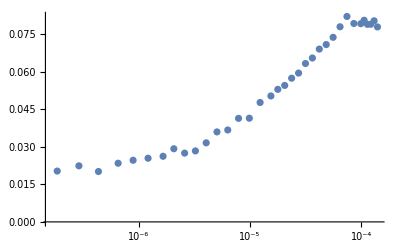

```mathematica
datac3=Transpose[{10^-9*{140270,130919,122191,114045,106442,99346,86096,74617,64668,56046,48573,42096,36484,31619,27403,23749,20583,17838,15460,12368,9894,7916,6332,5066,4053,3242,2594,2075,1660,1217,893,655,436,291,185.7},10^-2*{7.78926,8.0349,7.8978,7.8934,8.05567,7.919129,7.92697,8.208,7.7963,7.37448,7.08522,6.90513,6.54825,6.3273,5.9460,5.74112,5.4518,5.2956,5.03227,4.771144,4.1435,4.1368,3.6724,3.5956,3.1592,2.8359,2.748,2.9226,2.6213,2.5442,2.46215,2.3436,2.0131,2.2403,2.0309}} ];(*Concentration of GR in Molar versus anisotropy*)
ListLogLinearPlot[datac3,PlotRange->All]
```

```mathematica
Export["201600826_C3NTD-TSGcc.csv",N[datac3]]
```

201600826_C3NTD-TSGcc.csv

#### One Binding Site:

```mathematica
fit[bu_,bb_,x_,kd_]:=bu*1/(1+x/kd)+bb*(x/kd)/(1+x/kd);
nlm=NonlinearModelFit[datac3,fit[bu,bb,x,kd],{{bu,0.02},{bb,0.06},{kd,2*10^-5}},x]
```

FittedModel[0.0205479/(1+48701.8 x)+(4447.53 x)/(1+48701.8 x)]

{bu→0.0205479,bb→0.0913217,kd→0.0000205331}

{0.000735555,0.00128397,1.44737×10^-6}

0.99885

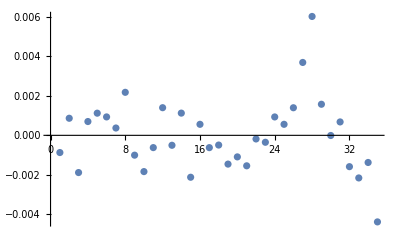

```mathematica
nlm["BestFitParameters"]
nlm["ParameterErrors"]
nlm["AdjustedRSquared"]
ListPlot[Reverse[nlm["FitResiduals"]]]
```

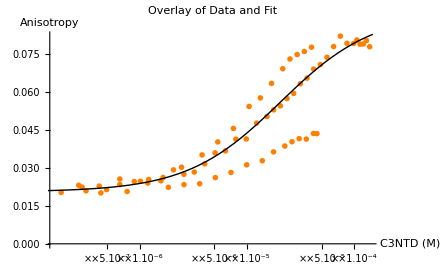

```mathematica
Show[ListLogLinearPlot[{datac3,data,abridgeddata},PlotRange->All,PlotTheme->"Monochrome",PlotStyle->{Directive[PointSize[Medium],Orange]},AxesLabel->{"C3NTD (M)","Anisotropy"},PlotLabel->"Overlay of Data and Fit"],LogLinearPlot[nlm[x],{x,1*10^-7,1.5*10^-4},PlotTheme->"Monochrome",PlotStyle->Thick]]
```

Overlay of my rss experiments with SEC pure C3NTD. Note that one experiment with less pure protein (2nd Ni column) looks a bit different--higher rss and higher Kd ~30µM.

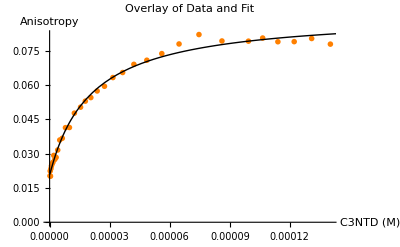

```mathematica
Show[ListPlot[datac3,PlotRange->All,PlotTheme->"Monochrome",PlotStyle->{Directive[PointSize[Medium],Orange]},AxesLabel->{"C3NTD (M)","Anisotropy"},PlotLabel->"Overlay of Data and Fit"],Plot[nlm[x],{x,1*10^-7,1.5*10^-4},PlotTheme->"Monochrome",PlotStyle->Thick]]
```

Calculation of interaction energy, by -RT*ln Ka  =  -RT*ln (Kd^-1):

```mathematica
-R*288.15*Log[(0.0000205331)^-1]
```

-6179.85

#### Two Identical Binding Sites:

```mathematica
fit2[bu_,bb_,x_,kd_]:=bu*1/(1+2*x/kd+x^2/kd^2)+0.5*bb*(2*x/kd)/(1+2*x/kd+x^2/kd^2)+bb*(x^2/kd^2)/(1+2*x/kd+x^2/kd^2);
nlm2=NonlinearModelFit[datac3,fit2[bu,bb,x,kd],{{bu,0.02},{bb,0.06},{kd,1*10^-5}},x]
```

FittedModel[0.0207665/(1+131621. x+4.331×10^9 x^2)+(«18»«1»«1»)/(«1»)+(3.93535×10^8 «1»)/(1+«19» x+«21» x^2)]

{bu→0.0207665,bb→0.0908647,kd→0.0000151952}

{0.00073628,0.00123486,9.84657×10^-7}

0.998872

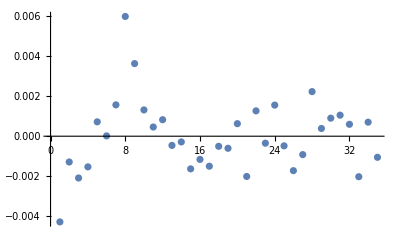

```mathematica
nlm2["BestFitParameters"]
nlm2["ParameterErrors"]
nlm2["AdjustedRSquared"]
ListPlot[nlm2["FitResiduals"]]
```

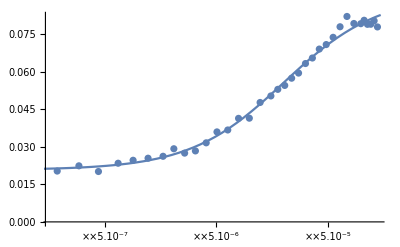

```mathematica
Show[ListLogLinearPlot[datac3,PlotRange->All],LogLinearPlot[nlm2[x],{x,1*10^-7,1.5*10^-4}]]
```

#### Two Dependent binding sites:

```mathematica
fit3[bu_,bb_,x_,kd1_,kd2_]:=bu*1/(1+2*x/kd1+x^2/kd2^2)+0.5*bb*(2*x/kd1)/(1+2*x/kd1+x^2/kd2^2)+bb*(x^2/kd2^2)/(1+2*x/kd1+x^2/kd2^2);
nlm3=NonlinearModelFit[datac3,fit3[bu,bb,x,kd1,kd2],{{bu,0.02},{bb,0.06},{kd1,1*10^-5},{kd2,2*10^-5}},x]
```

FittedModel[0.0213283/(1+115635. x+4.35864×10^9 x^2)+(«17»«1»«1»)/(«1»)+(3.90614×10^8 «1»)/(1+«19» x+«21» x^2)]

{bu→0.0213283,bb→0.0896184,kd1→0.0000172959,kd2→0.0000151469}

{0.000942032,0.00190095,2.85438×10^-6,9.24204×10^-7}

0.998864

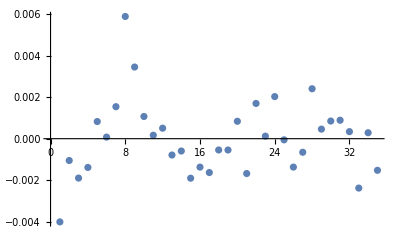

```mathematica
nlm3["BestFitParameters"]
nlm3["ParameterErrors"]
nlm3["AdjustedRSquared"]
ListPlot[nlm3["FitResiduals"]]
```

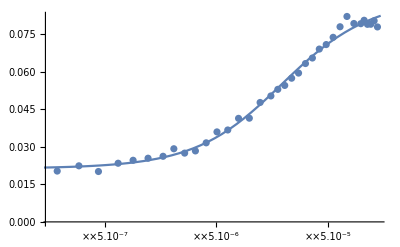

```mathematica
Show[ListLogLinearPlot[datac3,PlotRange->All],LogLinearPlot[nlm3[x],{x,1*10^-7,1.5*10^-4}]]
```

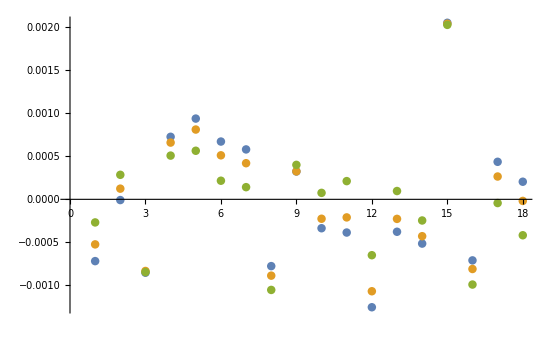

```mathematica
ListPlot[{nlm["FitResiduals"],nlm2["FitResiduals"],nlm3["FitResiduals"]}]
```

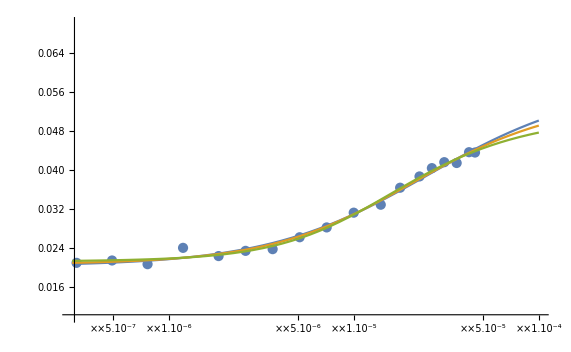

```mathematica
Show[ListLogLinearPlot[data,PlotRange->{{3*10^-7,1*10^-4},{0.01,0.07}}],LogLinearPlot[{nlm[x],nlm2[x],nlm3[x]},{x,3*10^-7,1*10^-4}]]
```

I need to go to a higher concentration to really distinguish these models. About 80 µM may be sufficient.

#### 2:2 Binding Scheme:

Kd = (TSG^2*GR^2)/TSG2xGR2; assume GR_unbound is roughly GR_Total, probably reasonable here (TSG @76 nM).
TSG_T=TSG_Unbound+2*TSG_Bound
Kd == ((TSG_T-2*TSG_Bound)^2*GR^2)/TSG_Bound
TSG_Bound*K_d== (TSG_T-2*TSG_Bound)^2*GR^2
0== (TSG_T-2*TSG_Bound)^2*GR^2-TSG_Bound*K_d

```mathematica
Solve[0==(tsg-2*bound)^2*gr^2-bound*kd,bound]
```

{{bound→(kd+4 gr^2 tsg-√kd √(kd+8 gr^2 tsg))/(8 gr^2)},{bound→(kd+4 gr^2 tsg+√kd √(kd+8 gr^2 tsg))/(8 gr^2)}}

```mathematica
f1[kd_,tsg_,gr_]:=(kd+4 gr^2 tsg-√kd √(kd+8 gr^2 tsg))/(8 gr^2);
f2[kd_,tsg_,gr_]:=(kd+4 gr^2 tsg+√kd √(kd+8 gr^2 tsg))/(8 gr^2);
```

```mathematica
f1[(1.0*10^-5)^3,10^-8,10^-4]
f2[(1.0*10^-5)^3,10^-8,10^-4]
```

7.2949×10^-10

3.42705×10^-8

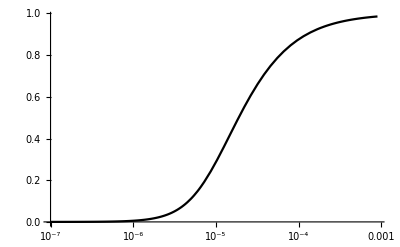

```mathematica
LogLinearPlot[fit[(3.0*10^-6)^3,7.6*10^-8,gr,1,0],{gr,10^-7,9*10^-4},PlotTheme->"Monochrome",PlotRange->All]
```

Asymmetric, with a sharp low concentration critical point and a weaker high concentration critical point.

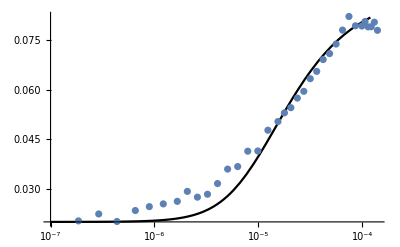

```mathematica
Show[LogLinearPlot[fit[(3.0*10^-6)^3,7.6*10^-8,gr,0.089,0.02],{gr,10^-7,1.2*10^-4},PlotTheme->"Monochrome",PlotRange->All],ListLogLinearPlot[datac3]]
```

```mathematica
fit[kd_,tsg_,gr_,bb_,bu_]:=bb*(2*f1[kd,tsg,gr])/tsg+bu*(1-(2*f1[kd,tsg,gr])/tsg);
```

```mathematica
2*f1[(6.0*10^-6)^3,7.6*10^-8,10^-4]/(7.6*10^-8)*0.089
```

0.0611827

```mathematica
nlmTwobyTwoHandsOfBlue=NonlinearModelFit[datac3,{fit[kd,7.6*10^-8,gr,bb,bu],kd>0},{{kd,(6.0*10^-6)^3},{bb,0.089},{bu,0.02}},gr]
```

NonlinearModelFit::acceptlev: Solved to acceptable level.

FittedModel[(14625.5 (0.0585166+«1»-«19» √(«1»)))/gr^2+0.00448656 (1-(«22» («1»))/gr^2)]

{kd→0.0585166,bb→0.00444614,bu→0.00448656}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{1956.77,0.00961706,0.00959555}

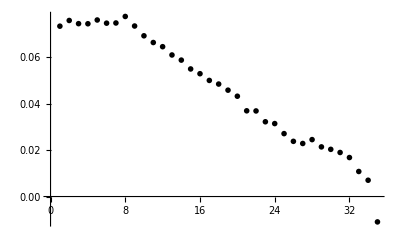

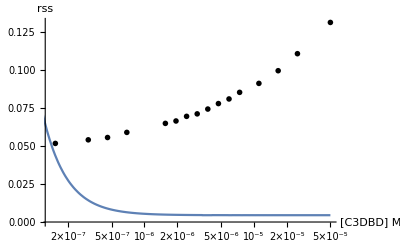

0.0947778

```mathematica
nlmTwobyTwoHandsOfBlue["BestFitParameters"]
nlmTwobyTwoHandsOfBlue["ParameterErrors"]
ListPlot[nlmTwobyTwoHandsOfBlue["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[dataAvgC3,PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fit[kd,7.6*10^-8,gr,bb,bu]/.nlmTwobyTwoHandsOfBlue["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmTwobyTwoHandsOfBlue["FitResiduals"]^2]
```

Cannot describe the data in any reasonable manner.

#### Hill plot analysis

First, calculate fractional saturation, theta, based on fitted bound and unbound baselines:

```mathematica
theta=(Flatten[Take[Transpose[data],-1]]-0.020267687639493426)/(0.05757655792340063-0.020267687639493426)
```

{0.623989,0.625801,0.566469,0.570991,0.538299,0.492653,0.430709,0.337301,0.293587,0.212556,0.158603,0.0932302,0.0838758,0.0552221,0.10036,0.0107029,0.0309662,0.0179666}

```mathematica
Plot ln(theta / (1-theta)) versus ln (x)
```

```mathematica
hill=N[Transpose[{Log[Flatten[Take[Transpose[data],1]]],Log[theta]-Log[1-theta]}]]
```

{{-10.0049,0.506513},{-10.079,0.514243},{-10.2332,0.267458},{-10.3873,0.285894},{-10.5415,0.153495},{-10.6956,-0.0293917},{-10.9368,-0.278959},{-11.178,-0.675346},{-11.5144,-0.878024},{-11.8509,-1.30959},{-12.1874,-1.66866},{-12.5238,-2.27482},{-12.8604,-2.39081},{-13.1965,-2.83959},{-13.639,-2.19323},{-14.0808,-4.52648},{-14.5228,-3.4434},{-14.9644,-4.00111}}

FittedModel[10.339+0.979052 x]

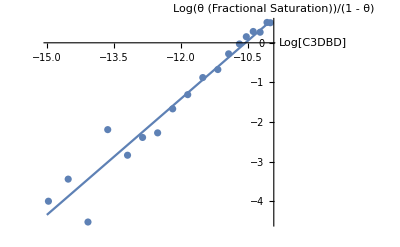

```mathematica
hillLine=LinearModelFit[hill,x,x]
Show[ListPlot[hill,AxesLabel->{"Log[C3DBD]","Log(θ (Fractional Saturation))/(1 - θ)"}],Plot[hillLine[x],{x,-15,-10}]]
```

Positive Hill coefficient of 1.17 using the fitted values for two independent sites to normalize the data.
Hill value of nearly 1 when I use the fitted baselines for one site binding.

Clearly, for this to be sensible, I would actually need to have a full binding curve and a good by-eye estimate of the baselines--independent of some fitted value.

Global Fitting of the above data and data from 2016-7-26 and 2016-8-8

## Set up:

2016-7-26

```mathematica
data2c3=Transpose[{10^-9*{40185,34444,29524,25306,21691,17043,13391,10521,7515,5368,3834,2465,1584,1019,655,421,271},10^-2*{7.7723,7.602,7.4805,7.3046,6.92098,6.3406,5.7672,5.4295,4.5606,4.02652,3.5142,3.0265,2.4894,2.4729,2.5612,2.2819,2.3131}} ];(*Concentration of GR in Molar versus anisotropy*)
```

2016-8-8

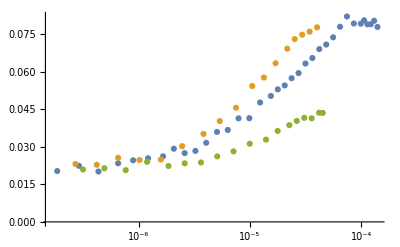

```mathematica
data3c3=Transpose[{10^-9*{45177,41950,35957,30820,26417,22644,17791,13979,9985,7132,5094,3639,2599,1857,1193,767,493,317},10^-2*{4.3548,4.36156,4.1402,4.15707,4.0351,3.8648,3.633695,3.2852,3.12211,2.81979,2.6185,2.3746,2.3397,2.232796,2.4012,2.0667,2.1423,2.0938}} ];(*Concentration of GR in Molar versus anisotropy*)
ListLogLinearPlot[{datac3,data2c3,data3c3},PlotRange->All]
```

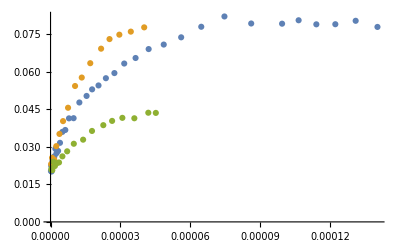

```mathematica
ListPlot[{datac3,data2c3,data3c3},PlotRange->All]
```

Now join the datasets and add some dummy variables to keep track of each dataset.

```mathematica
dataGlobalc3=Join[datac3/.{x_,y_}->{0,x,y},
data2c3/.{x_,y_}->{1,x,y},
data3c3/.{x_,y_}->{2,x,y}];
```

Below is our basic fitting function. It needs to be built up to accommodate the dummy variables.

```mathematica
fit[bu_,bb_,x_,kd_]:=bu*1/(1+x/kd)+bb*(x/kd)/(1+x/kd);
```

```mathematica
fitmodel[x_,bu_,bb0_,bb1_,bb2_,kd_,set_]:=Which[set==0,Evaluate@fit[bu,bb0,x,kd],
set==1,Evaluate@fit[bu,bb1,x,kd],
set==2,Evaluate@fit[bu,bb2,x,kd]];
```

The global model allows each fully bound baseline to fit individually, but the Kd and unbound baselines are shared.

## The fit:

```mathematica
globalFitc3=NonlinearModelFit[dataGlobalc3,fitmodel[x,bu,bb0,bb1,bb2,kd,set],{{bu,0.02},{bb0,0.08},{bb1,0.08},{bb2,0.04},{kd,2*10^-5}},{set,x}]
```

FittedModel[Which[set==0,(«21»)/(1+«1»)+(«1»)/(«1»),«1»,«1»,set==2,0.020356/(1+x/(«24»))+(0.0536076 x)/(0.0000196309 (1+«1»))]]

{bu→0.020356,bb0→0.0905737,bb1→0.110765,bb2→0.0536076,kd→0.0000196309}

{0.000419233,0.000968467,0.00212088,0.00109927,9.90854×10^-7}

0.998935

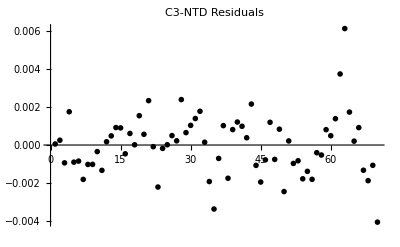

-1.97887×10^-6

```mathematica
globalFitc3["BestFitParameters"]
globalFitc3["ParameterErrors"]
globalFitc3["AdjustedRSquared"]
ListPlot[Reverse[globalFitc3["FitResiduals"]],PlotTheme->"Monochrome",PlotLabel->"C3-NTD Residuals"]
globalFitc3["ParameterErrors"][[5]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[globalFitc3["Response"]]-Length[globalFitc3["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

```mathematica
Export["C3-GlobalResiduals.csv",Reverse[globalFitc3["FitResiduals"]]]
```

C3-GlobalResiduals.csv

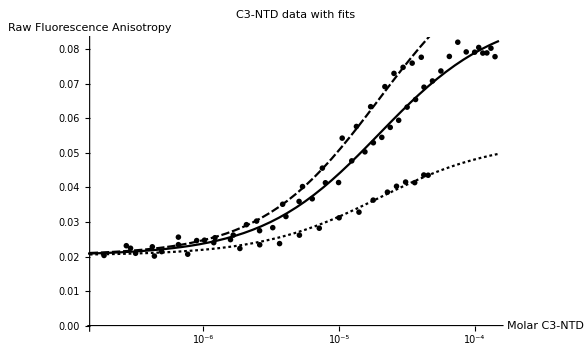

```mathematica
Show[ListLogLinearPlot[{datac3,data2c3,data3c3},PlotRange->All,PlotTheme->"Monochrome",PlotLabel->"C3-NTD data with fits",AxesLabel->{"Molar C3-NTD","Raw Fluorescence Anisotropy"}],LogLinearPlot[{fit[bu,bb0,x,kd]/.globalFitc3["BestFitParameters"],fit[bu,bb1,x,kd]/.globalFitc3["BestFitParameters"],fit[bu,bb2,x,kd]/.globalFitc3["BestFitParameters"]},{x,10^-7,1.5*10^-4},PlotTheme->"Monochrome"]]
```

Plot C3 and A NTD data together.

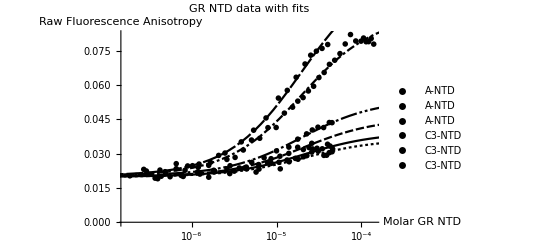

```mathematica
Show[ListLogLinearPlot[{data,data2,data3,datac3,data2c3,data3c3},PlotRange->All,PlotTheme->"Monochrome",PlotLabel->"GR NTD data with fits",AxesLabel->{"Molar GR NTD","Raw Fluorescence Anisotropy"},PlotLegends->{"A-NTD","A-NTD","A-NTD","C3-NTD","C3-NTD","C3-NTD"}],LogLinearPlot[{fit[bu,bb0,x,kd]/.globalFit["BestFitParameters"],fit[bu,bb1,x,kd]/.globalFit["BestFitParameters"],fit[bu,bb2,x,kd]/.globalFit["BestFitParameters"],fit[bu,bb0,x,kd]/.globalFitc3["BestFitParameters"],fit[bu,bb1,x,kd]/.globalFitc3["BestFitParameters"],fit[bu,bb2,x,kd]/.globalFitc3["BestFitParameters"]},{x,10^-7,5*10^-4},PlotTheme->"Monochrome"]]
```

Normalize the C3 data to the fraction bound: (data - unbound baseline) / (bound baseline - unbound baseline)

```mathematica
datac3Norm=Transpose[{Transpose[datac3][[1]],(Transpose[datac3][[2]]-0.020356003012164635)/(0.09057371772597482-0.020356003012164635)}];
```

```mathematica
data2c3Norm=Transpose[{Transpose[data2c3][[1]],(Transpose[data2c3][[2]]-0.020356003012164635)/(0.11076538589942467-0.020356003012164635)}];
```

```mathematica
data3c3Norm=Transpose[{Transpose[data3c3][[1]],(Transpose[data3c3][[2]]-0.020356003012164635)/(0.05360758710990357-0.020356003012164635)}];
```

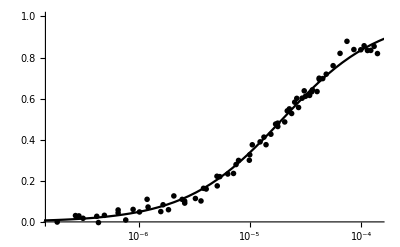

```mathematica
c3GlobalNorm=Flatten[{datac3Norm,data2c3Norm,data3c3Norm},1];
Show[ListLogLinearPlot[c3GlobalNorm,PlotTheme->"Monochrome",PlotRange->{Automatic,{0,1}}],LogLinearPlot[(x/0.000019630864347760185)/(1+x/0.000019630864347760185),{x,10^-7,1.7*10^-4},PlotTheme->"Monochrome"]]
```

```mathematica
SetDirectory["/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy

```mathematica
Export["C3_GlobalDATA-Normalized.csv",N[c3GlobalNorm]]
```

C3_GlobalDATA-Normalized.csv

```mathematica
normResiduals=Transpose[{Transpose[c3GlobalNorm][[1]],Transpose[c3GlobalNorm][[2]]-(Transpose[c3GlobalNorm][[1]]/0.000019630864347760185)/(1+Transpose[c3GlobalNorm][[1]]/0.000019630864347760185)}];
```

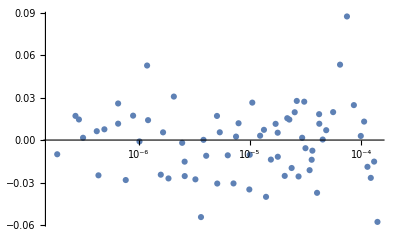

```mathematica
ListLogLinearPlot[normResiduals]
```

```mathematica
Export["C3-GlobalResiduals-NormdDATA.csv",N[normResiduals]]
```

C3-GlobalResiduals-NormdDATA.csv